# Visualizing the solar spectrum

In this notebook, we examine the solar spectrum (technically, solar spectral irradiance), and use it to find the central wavelength of the solar spectrum for calculations.

```mathematica
SolarSpectralIrradiance[wavelength_] := ResourceFunction["SolarIrradianceData"]["SurfaceIrradiance",Quantity[wavelength,"Nanometers"]] (* Define function to get solar spectrum *)
```

```mathematica
SolarSpectralIrradiance[500]
```

1.5451 W/(m^2 nm)

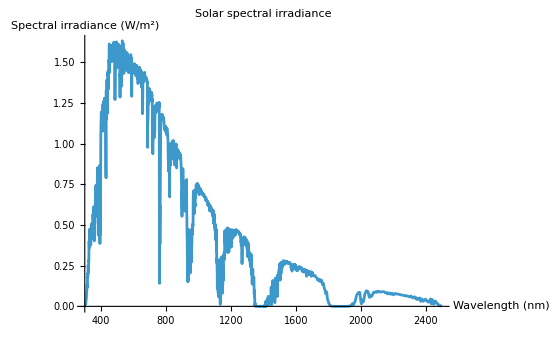

```mathematica
Plot[SolarSpectralIrradiance[wavelength], {wavelength, 300, 2500}, PlotLabel->"Solar spectral irradiance", AxesLabel->{"Wavelength (nm)", "Spectral irradiance (W/m^2)"}]
```

Now we integrate to find the average spectral irradiance, from which we can graphically find the central wavelength, as follows:

```mathematica
AvgSpectralIrradiance = NIntegrate[SolarSpectralIrradiance[wavelength],
 {wavelength, 300, 2500}]/(2500 - 300)
```

ResourceFunction::usermessage: SolarIrradianceData

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in wavelength near {wavelength} = {953.091}. NIntegrate obtained 993.474 and 1.41565 for the integral and error estimates.

0.451579 W/(m^2 nm)

This corresponds graphically to a central wavelength of about 393.7 nm (in the violet range).